## Defining Functions

Hello and welcome to our first lecture on Functions. In this lecture we will learn how to define functions.

### Introduction

Let’s define a simple function and break down its components.

```mathematica
square[x_]:=x^2
```

The name of the function is square. The argument is a named pattern, which in this case matches anything, hence the blank, that we named “x”. The := is our SetDelayed operator. And the right hand side is the function definition.

To use the function we evaluate:

```mathematica
square[3]
```

9

When we evaluate square[3], Mathematica evaluates the right hand side of the expression with x = 3.

In general, you will almost always want to define functions using SetDelayed.

Notice that like any other Mathematica expression, this expression has a Head, which in this case is square, and it also has argument(s).

### Fibonacci Numbers

Let’s write a program to compute the nth Fibonacci number. The Fibonacci sequence is a series of numbers that begin with the sequence {1, 1}. The next number in the sequence is equal to the sum of the previous two. So for example the first 10 numbers in the sequence, using Mathematica’s built in Fibonacci function are:

```mathematica
?Fibonacci
```

RowBox[{"Fibonacci", "[", StyleBox["n", "TI"], "]"}] gives the Fibonacci number SubscriptBox[StyleBox["F", "TI"], StyleBox["n", "TI"]]. 
RowBox[{"Fibonacci", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the Fibonacci polynomial RowBox[{SubscriptBox[StyleBox["F", "TI"], StyleBox["n", "TI"]], "(", StyleBox["x", "TI"], ")"}].

```mathematica
Table[Fibonacci[n],{n,1,10}]
```

{1,1,2,3,5,8,13,21,34,55}

We will write our own function to compute the Fibonacci sequence. Notice the sequence is defined by a recurrence relation:

F_n=F_(n-1)+F_(n-2)
F_1=1
F_2=2

A convenient way to define a recurrence relation is to use a recursive function. A recursive function is a function that calls itself. Here’s how we define it:

```mathematica
fib[n_]:=fib[n-1]+fib[n-2]
```

Now we need to define the seed values. These will also serve as the terminating condition for the recursion. Otherwise, the recursive function would call itself infinitely many times.

```mathematica
fib[1]:=1
```

```mathematica
fib[2]:=1
```

Now we can call:

```mathematica
fib[1]
```

1

```mathematica
fib[2]
```

1

Calling fib[1] and fib[2] match the terminating conditions, so they return their corresponding values.

```mathematica
fib[3]
```

2

When you call fib[3], Mathematica evaluates the right hand side of the recurrence relation, which calls fib[1] and fib[2]. These return 1 + 1, and the result is 2.

```mathematica
fib[4]
```

3

When you call fib[4], Mathematica evaluates fib[3] + fib[2], which evaluate as we saw above.

Let’s look at the first 12 values in the Fibonacci sequence:

```mathematica
Table[fib[n],{n,1,12}]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

Let’s look at the definition of our function:

```mathematica
?fib
```

Global`fib

fib[1]:=1
 
fib[2]:=1
 
fib[n_]:=fib[n-1]+fib[n-2]

We have a small bug in our program. Can you guess what it might be?

The problem with our recursive function is that it will only terminate for positive integer values, but anything will match the pattern of our function argument, because blank matches everything:

```mathematica
fib[3.5]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of fib[-1018.5-1].

Hold[fib[3.5-1]+fib[3.5-2]]

Here, Mathematica is saying that it reached the recursion limit of 1024. This occurred because:

fib[3.5] = fib[2.5] + fib[1.5]
fib[2.5] = fib[1.5] + fib[0.5]
fib[1.5] = fib[0.5] + fib[-0.5]
fib[0.5] = fib[-0.5] + fib[-1.5]

As you can see, the recursion will never terminate. Mathematica automatically stops at 1024.

In the first place, we don’t want our fib function to be called on anything other than positive integers. Let’s redefine our fib function so that it only works on positive integers:

First, let’s clear the definition of fib using the Clear function so that we don’t have the old fib hanging around:

```mathematica
?Clear
```

RowBox[{"Clear", "[", RowBox[{SubscriptBox[StyleBox["symbol", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["symbol", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] clears values and definitions for the SubscriptBox[StyleBox["symbol", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Clear", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_1\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"form\",\"TI\"]\_2\)\"", ShowStringCharacters->True], ",", StyleBox["…", "TR"]}], "]"}] clears values and definitions for all symbols whose names match any of the string patterns SubscriptBox[StyleBox["form", "TI"], StyleBox["i", "TI"]].

```mathematica
Clear[fib]
```

This cleared all definitions of fib, so we have to define our terminating conditions once again:

```mathematica
fib[1]:=1
```

```mathematica
fib[2]:=1
```

Now we can define the recursive part of the function, but instead of just n_, we use a pattern condition to limit what expressions match our pattern:

```mathematica
fib[n_Integer/;n>2]:=fib[n-1]+fib[n-2]
```

Our fib function is now defined such that it will only be evaluated if n is an Integer whose value is greater than 2. Let’s verify that it doesn’t do anything to non integers:

```mathematica
fib[3.5]
```

fib[3.5]

How about negative numbers:

```mathematica
fib[-3]
```

fib[-3]

Let’s also make sure it still works as it should:

```mathematica
Table[fib[n],{n,1,12}]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

Isn’t that neat? Mathematica’s function definition is really powerful, because we can specify what classes of expressions our function can accept. You should always think about the assumptions you make when you write a function, and you should try to express your assumptions as patterns so that your functions are only called on valid expressions, the same way we did with our fib function.

### Sin’s Taylor Series Expansion

Let’s look at another example. We will define the Sine function in terms of its Taylor series expansion. Here is the definition.

The arguments to our function are x, which is the value of sine we want to compute and N, which is the number of terms in the expansion. Let’s use table to generate the first 7 terms:

```mathematica
Table[(-1)^n x^(2 n+1)/(2n+1)!,{n,0,6}]
```

{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880,-x^11/39916800,x^13/6227020800}

To add all the terms together, we can use the Total function:

```mathematica
?Total
```

RowBox[{"Total", "[", StyleBox["list", "TI"], "]"}] gives the total of the elements in StyleBox["list", "TI"]. 
RowBox[{"Total", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] totals all elements down to level StyleBox["n", "TI"]. 
RowBox[{"Total", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", StyleBox["n", "TI"], "}"}]}], "]"}] totals elements at level StyleBox["n", "TI"]. 
RowBox[{"Total", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] totals elements at levels SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]] through SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]].

```mathematica
Total[Table[(-1)^n x^(2 n+1)/(2n+1)!,{n,0,6}]]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

Great, now let’s write the mySin function which will evaluate this expression at x:

```mathematica
mySin[x_,N_Integer?Positive]:=Total[Table[(-1)^i x^(2 i+1)/(2i+1)!,{i,0,N}]]
```

Here, we restrict number of terms to be a positive integer. Let’s make the default number of terms equal to 6:

```mathematica
mySin[x_]:=mySin[x,6]
```

Basically, we define mySin[x] to call the mySin[x, N] definition with N equal to 6.

```mathematica
mySin[x]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

Great! Let’s have some fun. Let’s plot our mySin function along side the built in Sin function:

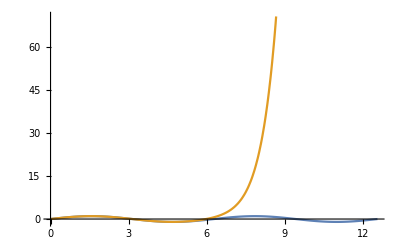

```mathematica
Plot[{Sin[x],mySin[x]},{x,0,4Pi}]
```

Let’s limit the range:

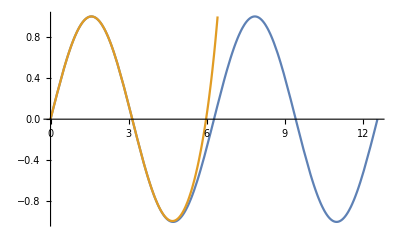

```mathematica
Plot[{Sin[x],mySin[x]},{x,0,4Pi},PlotRange->{Automatic,{-1,1}}]
```

Here our function doesn’t match the built in function well for larger values of x, because we are only approximating it with 6 terms in the series. Let’s also plot the error:

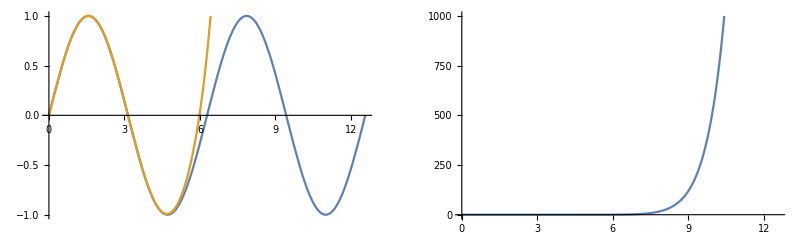

```mathematica
GraphicsRow[{
Plot[{Sin[x],mySin[x]},{x,0,4Pi},PlotRange->{Automatic,{-1,1}}],
Plot[Abs[Sin[x]-mySin[x]],{x,0,4Pi},PlotRange->{Automatic,{0,1000}}]
}]
```

Now guess what we’re gonna do. Did you guess?

We’re gonna wrap it in a Manipulate so that we can explore how the number of terms affects the error:

```mathematica
Manipulate[
GraphicsRow[{
Plot[{Sin[x],mySin[x,N]},{x,0,4Pi},PlotRange->{Automatic,{-1,1}}],
Plot[Abs[Sin[x]-mySin[x,N]],{x,0,4Pi},PlotRange->{Automatic,{0,1000}}]
}],
{N,1,20,1}]
```

Here, you can see our approximation of the Sin function in orange. As we increase the value of N, our mySin function approximates the real Sin function better and better, and the point where the error function diverges moves higher and higher.

### Summary

This concludes our first lecture on functions!